```mathematica
(*Mathematica*)
```

```mathematica
(*( D7 is SO(142): g#=14*13/2=91*)
```

```mathematica
(* graph models od D_7 type polyhedrons:two edge groups 7 fold rotations:91 and 21*)
```

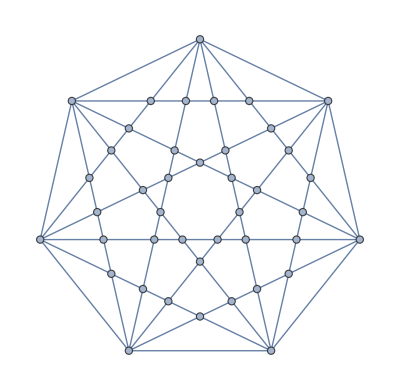
```mathematica
{91,42,51,{"DiagonalIntersection",7},-Graphics-,-Graphics3D-};
```

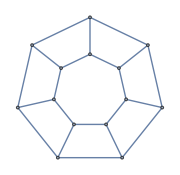
```mathematica
{21,14,9,{"Prism",7},-Graphics-,-Graphics3D-};
```

```mathematica
(* Point group Character table traces as Killing vectors: :<D_7:{a,b}:{1,a,b,b^2,b^3}>*)
```

```mathematica
(*John D. Dixon:Problems in Group Theory page 159*)
```

```mathematica
(* D_7 point group is not in the classical point group character tables*)
```

```mathematica
(*Fuchsian extended  Triange group <2,3,7,42> is hyperbolic*)
```

```mathematica
(* D_7 2x2 generators: x={{0,1},{1,0}}:y={{ϵ,0},{0,ϵ^(-1)}}:ϵ=Exp[2*Pi*I/7]*)
```

```mathematica
(*T(1,1):2x2 generators: x={{2,1},{1,0}}:y={{ϵ,0},{2,ϵ^(-1)}};g#=3*g-3+h=1: 1 dimensional disk*)
```

```mathematica
(* quadratic field:Q(Cos[Pi/7]): page 418 The Arithetic of Hyperbolic 3-Manifolds: Colin Maclachlan and Alan Reid*)
```

```mathematica
(*7Apollonian  as Kleinian group T[2,1]:g#=3*g-3+h=4*)
(*s[1]=N[{{1,0},{-2*I,1}}]
s[2]=N[{{Exp[2*Pi*I/7],-(1+Sqrt[7])/2},{0,Exp[-2*Pi*I/7]}}];
  s[3]=Inverse[s[1]]
s[4]=Inverse[s[2]]*)
```

```mathematica
ϵ=Exp[2*Pi*I/7]
```

ⅇ^((2 ⅈ π)/7)

```mathematica
s[1]={1,1,1,1,1}
```

{1,1,1,1,1}

```mathematica
s[2]={1,-1,1,1,1}
```

{1,-1,1,1,1}

```mathematica
s[3]={2,0,ϵ+ϵ^6,ϵ^2+ϵ^5,ϵ^3+ϵ^4}
```

{2,0,ⅇ^(-(2 ⅈ π)/7)+ⅇ^((2 ⅈ π)/7),ⅇ^(-(4 ⅈ π)/7)+ⅇ^((4 ⅈ π)/7),ⅇ^(-(6 ⅈ π)/7)+ⅇ^((6 ⅈ π)/7)}

```mathematica
s[4]={2,0,ϵ^2+ϵ^5,ϵ^3+ϵ^4,ϵ+ϵ^6}
```

{2,0,ⅇ^(-(4 ⅈ π)/7)+ⅇ^((4 ⅈ π)/7),ⅇ^(-(6 ⅈ π)/7)+ⅇ^((6 ⅈ π)/7),ⅇ^(-(2 ⅈ π)/7)+ⅇ^((2 ⅈ π)/7)}

```mathematica
s[5]={2,0,ϵ^3+ϵ^4,ϵ+ϵ^6,ϵ^2+ϵ^5}
```

{2,0,ⅇ^(-(6 ⅈ π)/7)+ⅇ^((6 ⅈ π)/7),ⅇ^(-(2 ⅈ π)/7)+ⅇ^((2 ⅈ π)/7),ⅇ^(-(4 ⅈ π)/7)+ⅇ^((4 ⅈ π)/7)}

```mathematica
va=Rationalize[N[Table[s[i].s[i],{i,5}]]]
```

{5,5,9,9,9}

```mathematica
(*Casimir invariant*)
```

```mathematica
ci=Rationalize[N[Sum[s[i].s[i],{i,5}]]//Chop]
```

37

```mathematica
(* State probability*)
```

```mathematica
pi=va/ci//Chop
```

{5/37,5/37,9/37,9/37,9/37}

```mathematica
Apply[Plus,pi]
```

1

```mathematica
(* Character table matrix*)
```

```mathematica
v=Table[s[i],{i,5}]
```

{{1,1,1,1,1},{1,-1,1,1,1},{2,0,ⅇ^(-(2 ⅈ π)/7)+ⅇ^((2 ⅈ π)/7),ⅇ^(-(4 ⅈ π)/7)+ⅇ^((4 ⅈ π)/7),ⅇ^(-(6 ⅈ π)/7)+ⅇ^((6 ⅈ π)/7)},{2,0,ⅇ^(-(4 ⅈ π)/7)+ⅇ^((4 ⅈ π)/7),ⅇ^(-(6 ⅈ π)/7)+ⅇ^((6 ⅈ π)/7),ⅇ^(-(2 ⅈ π)/7)+ⅇ^((2 ⅈ π)/7)},{2,0,ⅇ^(-(6 ⅈ π)/7)+ⅇ^((6 ⅈ π)/7),ⅇ^(-(2 ⅈ π)/7)+ⅇ^((2 ⅈ π)/7),ⅇ^(-(4 ⅈ π)/7)+ⅇ^((4 ⅈ π)/7)}}

```mathematica
ka=N[v.Transpose[v]]//Chop
```

{{5.,3.,1.,1.,1.},{3.,5.,1.,1.,1.},{1.,1.,9.,2.,2.},{1.,1.,2.,9.,2.},{1.,1.,2.,2.,9.}}

```mathematica
kb=N[Transpose[v].v]//Chop
```

{{14.,0,0,0,0},{0,2.,0,0,0},{0,0,7.,0,0},{0,0,0,7.,0},{0,0,0,0,7.}}

```mathematica
(* Cartan matrix from Killing vectors*)
```

```mathematica
ca=N[Table[2*s[i].s[j]/(s[i].s[i]),{i,5},{j,5}]]//Chop
```

{{2.,1.2,0.4,0.4,0.4},{1.2,2.,0.4,0.4,0.4},{0.222222,0.222222,2.,0.444444,0.444444},{0.222222,0.222222,0.444444,2.,0.444444},{0.222222,0.222222,0.444444,0.444444,2.}}

```mathematica
Det[ca]//Chop
Tr[ca]
```

16.863

10.

```mathematica
TableForm[ca]
```

2. | 1.2 | 0.4 | 0.4 | 0.4
1.2 | 2. | 0.4 | 0.4 | 0.4
0.222222 | 0.222222 | 2. | 0.444444 | 0.444444
0.222222 | 0.222222 | 0.444444 | 2. | 0.444444
0.222222 | 0.222222 | 0.444444 | 0.444444 | 2.

```mathematica
(*characteristic polynomial*)
```

```mathematica
p[x_]=CharacteristicPolynomial[ca,x]//Chop
```

16.863-54.5466 x+65.8941 x^2-37.4341 x^3+10. x^4-x^5

```mathematica
rts=x/.NSolve[p[x]==0,x]
```

{0.8,1.55556,1.55556,2.29776,3.79112}

```mathematica
(* relative energy levels from the Eigenvalues*)
```

```mathematica
eg=Eigenvalues[ca]
```

```mathematica
Ceiling[{3.7911243385071765,2.297764550381713,1.5555555555555554,1.5555555555555554,0.7999999999999994}]
```

{4,3,2,2,1}

```mathematica
Apply[Plus,eg]/Length[eg]
```

2.

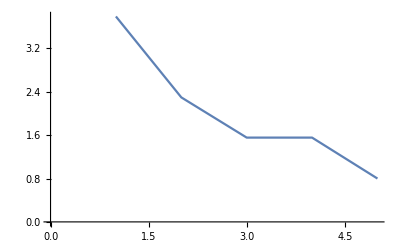

```mathematica
ListLinePlot[eg]
```

```mathematica
WeightedAdjacencyGraph[ca]
```

-Graphics-

```mathematica
aj=Table[If[ca[[i,j]]>0,1,0],{i,5},{j,5}]
```

{{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1}}

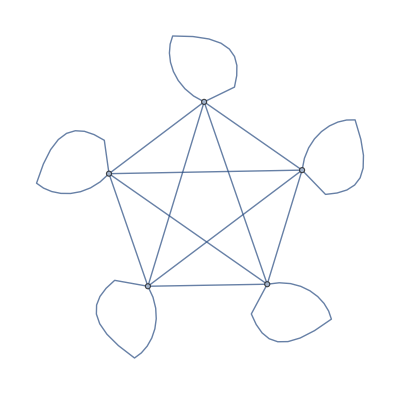

```mathematica
gr=AdjacencyGraph[aj]
```

```mathematica
GraphPlot3D[gr]
```

-Graphics3D-

```mathematica
E0=Table[(-1)^i*pi[[i]]*rts[[i]]*(-1)^j*pi[[j]]/(pi[[i]]*pi[[j]]),{i,5},{j,5}]
```

{{0.8+0. ⅈ,-0.8+0. ⅈ,0.8+0. ⅈ,-0.8+0. ⅈ,0.8+0. ⅈ},{-1.55556+0. ⅈ,1.55556+0. ⅈ,-1.55556+0. ⅈ,1.55556+0. ⅈ,-1.55556+0. ⅈ},{1.55556+0. ⅈ,-1.55556+0. ⅈ,1.55556+0. ⅈ,-1.55556+0. ⅈ,1.55556+0. ⅈ},{-2.29776+0. ⅈ,2.29776+0. ⅈ,-2.29776+0. ⅈ,2.29776+0. ⅈ,-2.29776+0. ⅈ},{3.79112+0. ⅈ,-3.79112+0. ⅈ,3.79112+0. ⅈ,-3.79112+0. ⅈ,3.79112+0. ⅈ}}

```mathematica
Ea=E0.Transpose[E0]
```

{{3.2+0. ⅈ,-6.22222+0. ⅈ,6.22222+0. ⅈ,-9.19106+0. ⅈ,15.1645+0. ⅈ},{-6.22222+0. ⅈ,12.0988+0. ⅈ,-12.0988+0. ⅈ,17.8715+0. ⅈ,-29.4865+0. ⅈ},{6.22222+0. ⅈ,-12.0988+0. ⅈ,12.0988+0. ⅈ,-17.8715+0. ⅈ,29.4865+0. ⅈ},{-9.19106+0. ⅈ,17.8715+0. ⅈ,-17.8715+0. ⅈ,26.3986+0. ⅈ,-43.5556+0. ⅈ},{15.1645+0. ⅈ,-29.4865+0. ⅈ,29.4865+0. ⅈ,-43.5556+0. ⅈ,71.8631+0. ⅈ}}

```mathematica
Eigenvalues[Ea]//Chop
```

{125.659,0,0,0,0}

```mathematica
q[x_]=ExpandAll[CharacteristicPolynomial[Ea,x]/x^4//Chop]
```

125.659-x

```mathematica
x/.NSolve[q[x]==0,x][[1]]
```

125.659

```mathematica
Sqrt[%]
```

11.2098

```mathematica
Transpose[E0].E0
```

{{25.1319+0. ⅈ,-25.1319+0. ⅈ,25.1319+0. ⅈ,-25.1319+0. ⅈ,25.1319+0. ⅈ},{-25.1319+0. ⅈ,25.1319+0. ⅈ,-25.1319+0. ⅈ,25.1319+0. ⅈ,-25.1319+0. ⅈ},{25.1319+0. ⅈ,-25.1319+0. ⅈ,25.1319+0. ⅈ,-25.1319+0. ⅈ,25.1319+0. ⅈ},{-25.1319+0. ⅈ,25.1319+0. ⅈ,-25.1319+0. ⅈ,25.1319+0. ⅈ,-25.1319+0. ⅈ},{25.1319+0. ⅈ,-25.1319+0. ⅈ,25.1319+0. ⅈ,-25.1319+0. ⅈ,25.1319+0. ⅈ}}

```mathematica
(*end*)
```